```mathematica
eventual[a_]:=Union[Drop[NestList[a #(1-#)&,Random[],1000],900],SameTest->(Chop[#1-#2]<10^-4&)]
```

```mathematica
logbif[low_,high_,inc_]:=ListPlot[Join@@Table[{a,#}&/@eventual[a],{a,low,high,inc}],PlotStyle->PointSize[Small],PlotRange->{{low,high},{0,1}},AspectRatio->1]
```

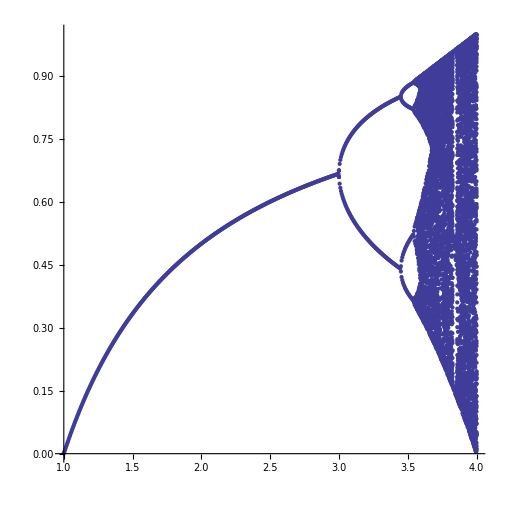

```mathematica
logbif[1,4,.005]
```

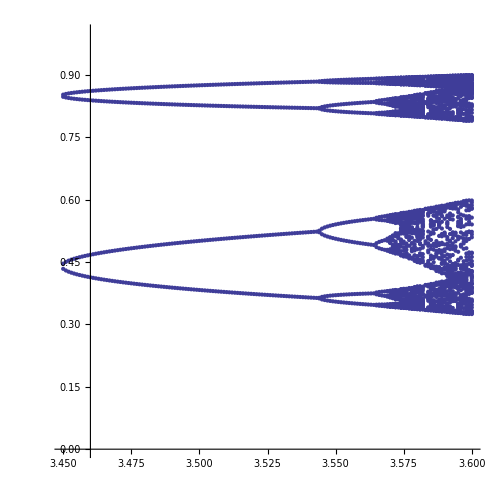

```mathematica
logbif[3.45,3.6,.001]
```

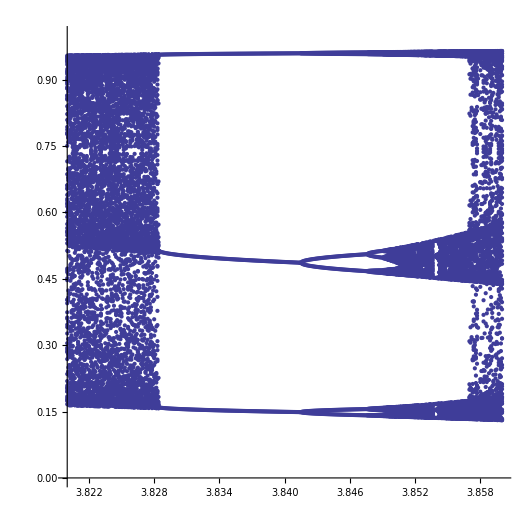

```mathematica
logbif[3.82,3.86,.0001]
```